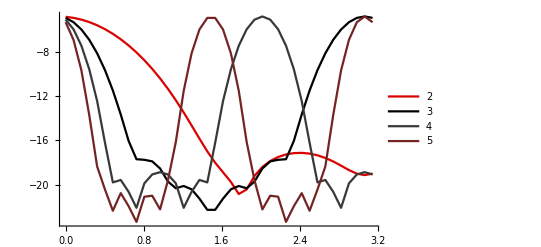

```mathematica
datos="/home/amaro/doc/carlos/cadena/datos6/";
masmatrices=Table[Import[datos<>"papa"<>ToString[i-1]<>".dat","Table"],{i,1,40}]/2^8;
eldichoso=Table[Flatten[Table[Log[10,Abs[masmatrices[[k]][[i]]]^2],{i,1,40}]],{k,1,40}];
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,2,5}];
Show[graficas,PlotRange->All]
```

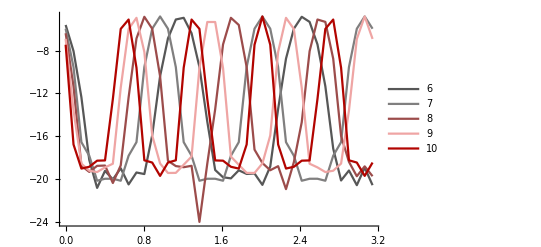

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,6,10}];
Show[graficas,PlotRange->All]
```

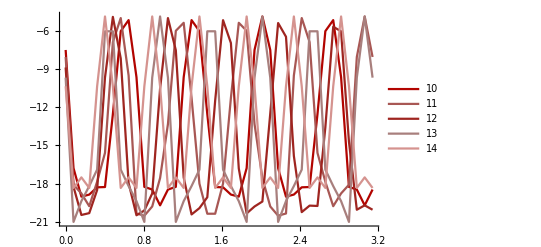

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,10,14}];
Show[graficas,PlotRange->All]
```